### Problem 3.1

```mathematica
SimpsonIntegrator[F_,a_,b_,n_] := Module[{Δx, Is},
If[Mod[n,2] ≠ 0,
Throw["n must be divisible by 2!"];
,
Δx = (b-a)/n;
Is = 0;
For[j=0, j ≤ n-2, j+=2,
Is = Is + (1/3) Δx (F[a + j Δx] + 4 F[a+(j+1)Δx] + F[a + (j+2)Δx]);
];
];
Return[Is];
]
```

```mathematica
IEstimate31 = SimpsonIntegrator[Sinc, 0, 2, 76];
```

```mathematica
N[IEstimate31,10]
```

1.605412977

### Problem 3.2

```mathematica
BField[x_,y_,z_,n_,R_] := Module[{F},
F[ϕ_] := {z Cos[ϕ], z Sin[ϕ], -(x Cos[ϕ] + y Sin[ϕ] - R)}/(((x - R Cos[ϕ])^2+(y-R Sin[ϕ])^2 + z^2)^(3/2));
Return[SimpsonIntegrator[F, 0, 2π, n]];
];
```

```mathematica
ActualMagField = 2π/((1+0.5^2)^(3/2))
```

4.49588

```mathematica
BField[0,0,0.5,4,1]
```

{0.,0.,4.49588}

Because this problem is rotationally symmetric, the number of grid points does not actually matter. Even 2 grid points gives the correct value for the z-direction---the only problem is an artifact in the x-direction that goes away with 4 grid points.

### Problem 3.3

```mathematica
BVals = Table[{{x,y,z},BField[x,y,z,10,1.]},{x,-2,2,0.25},{y, -2,2,0.25},{z,-0.5,0.5,1./π}];
```

```mathematica
ListVectorPlot3D[BVals]
```

-Graphics3D-

```mathematica
BVals2D = Table[{{y,z}, Drop[BField[0,y,z,10,0.1],1]}, {y, -2, 2, 0.25}, {z, -0.5, 0.5, 1./π}];
```

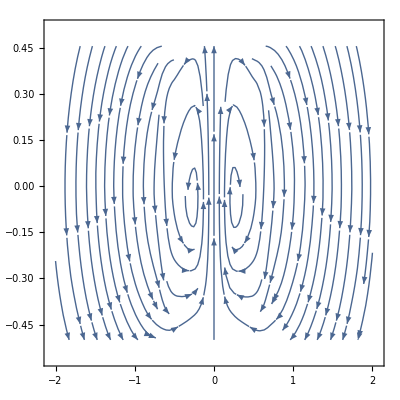

```mathematica
ListStreamPlot[BVals2D]
```